```mathematica
(*s=InputString["Enter xml file name","engine_visibility_saliency.xml"]//StringReplace[#," "->""]&;*)
xml=Import[NotebookDirectory[]<>"~images\\foot.xml"];
{tfifile,volumefile,legends,face,imagefilenames,featurefilename,resultxml,imagefile,dataname,plotpath,imagepath}=xml;
Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]
```

{Feature 1,Feature 2,Feature 3,Feature 4,Feature 5}
{right,top}
{D:\document\work\time-varying-visualization\~images\foot_saliency_chart.pdf,D:\document\work\time-varying-visualization\~images\foot_visibility_chart.pdf,D:\document\work\time-varying-visualization\~images\foot_visibility_saliency_brightness_chart.pdf,D:\document\work\time-varying-visualization\~images\foot_visibility_saliency_saturation_chart.pdf,D:\document\work\time-varying-visualization\~images\foot_visibility_saliency_weighted_chart.pdf}
D:\document\work\time-varying-visualization\~images\foot_visibility_saliency_feature.png
D:\document\work\time-varying-visualization\~images\saliency.xml
D:\document\work\time-varying-visualization\~images\foot.png
foot
D:\document\work\time-varying-visualization\~plot\
D:\document\work\time-varying-visualization\~images\

```mathematica
d0=Colorize[MorphologicalComponents[-Graphics3D-]];
```

```mathematica
d=ColorConvert[d0,"Grayscale"];
cl=MorphologicalComponents[d] ;
normalized=cl//Image3D//ImageAdjust;
pos=First@PixelValuePositions[normalized,#]&/@{0.2,0.4,0.6,0.8,1}
clusters={{2->0,3->0,4->0,5->0},{1->0,3->0,4->0,5->0},{1->0,2->0,4->0,5->0},{1->0,2->0,3->0,5->0},{1->0,2->0,3->0,4->0}};
```

{{95,104,128},{35,98,128},{87,97,128},{66,79,128},{48,69,128}}

{128,128,128}

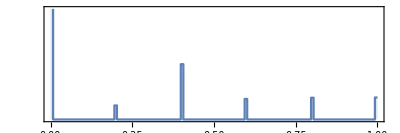

{7755.,30629.,11372.,12048.,12182.}

Export::chtype: First argument rawfile is not a valid file specification.

{RGBColor[{0.7725490196078432, 0.8509803921568627, 0.7333333333333333}],RGBColor[{0.8117647058823529, 0.22745098039215686, 0.8549019607843137}],RGBColor[{0.3764705882352941, 0.6313725490196078, 0.5843137254901961}],RGBColor[{0.7294117647058823, 0.7137254901960784, 0.7058823529411765}],RGBColor[{0.8431372549019608, 0.5882352941176471, 0.3411764705882353}]}

```mathematica
f:=#&;
ImageDimensions[d]
ImageHistogram[normalized]
features=Image3D@Clip[(cl/.#),{0,1}]&/@clusters;
N@ImageMeasurements[#,"TotalIntensity"]&/@features
Export[rawfile,Flatten@ImageData[normalized,"Byte"],{"Binary","Byte"}];
colorized=cl//Colorize;
chartcolors=RGBColor@PixelValue[colorized,#]&/@pos
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
Table[MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"_"<>face[[i]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face[[i]]]]]&,colorizedfeatures],{i,Length[face]}];
Export[StringReplace[imagefile,"."->"_"<>#<>"."],Show[colorized,Boxed->False,ViewPoint->viewpoints[#]]]&/@face;
```

```mathematica
top:=Module[{list,count,img,list2,list3,tmp},(* top *)
list=Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
```

```mathematica
back:=Module[{list,count,img,list2,list3,tmp},(* back *)
list=Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
```

```mathematica
left:=Module[{list,count,img,list2,list3,tmp},(* left *)
list=Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
```

```mathematica
bottom:=Module[{list,count,img,list2,list3,tmp},(* bottom *)
list=Reverse@Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
```

```mathematica
front:=Module[{list,count,img,list2,list3,tmp},(* front *)
list=Reverse@Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
```

```mathematica
right:=Module[{list,count,img,list2,list3,tmp},(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
```

```mathematica
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
{lightness,chroma,hue}=ColorSeparate[ColorConvert[colorized,"LCH"]];
opacity=ImageApply[f[#]&,d];
```

```mathematica
(*g1=ImageSubtract[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageSubtract[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageSubtract[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]]
g4=ImageSubtract[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]]*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];
(*diff=ImageSubtract[opacity,d3]//ImageAdjust;*)
(*r=ImageApply[{1,1,1,#2}*List@@rgbafunction[#1]&,{d,diff}]//Image3D[#,ColorSpace->"RGB"]&*)
(*dog1=ImageSubtract[GaussianFilter[opacity,2],GaussianFilter[opacity,4]];
dog2=ImageSubtract[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]]
Export[path<>"disks_saliency.png",dog2];*)
```

{0.284531,0.0572081,0.258996,0.237976,0.161289}

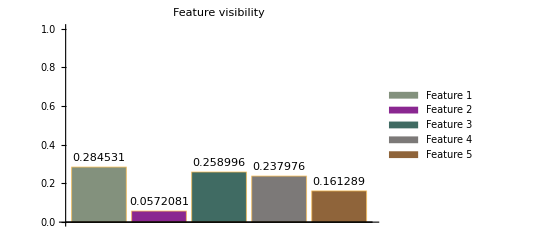

{0.0778709,0.159409,0.0774234,0.0956878,0.0895883}

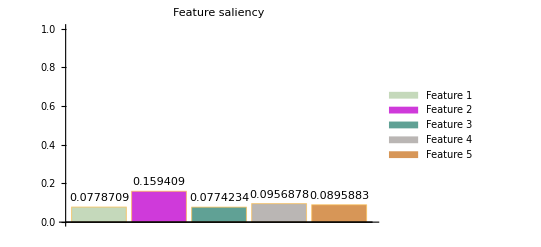

{0.375053,0.0436083,0.207036,0.234455,0.139848}

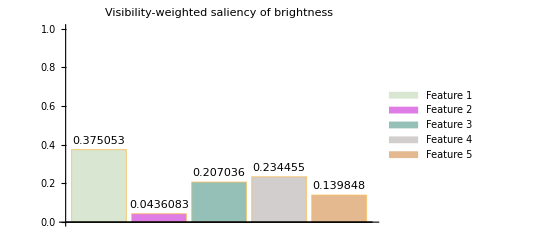

{0.222678,0.218237,0.243244,0.0185833,0.297258}

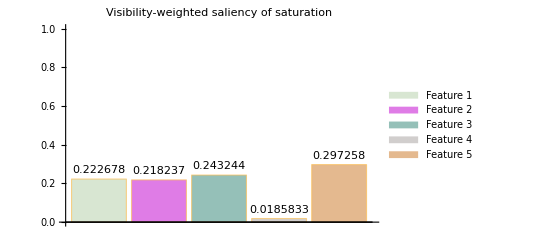

{0.298866,0.130923,0.22514,0.126519,0.218553}

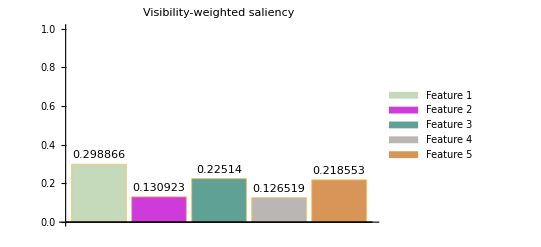

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of RegularExpression[https?://.*].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[Import::nffil :  File not found during Import.]

AssociateTo::invak: The argument scoremap is not a valid Association.

```mathematica
facename=First@face;
vis=renderslices[facename];
visibility=ParallelTable[ImageMeasurements[ImageMultiply[vis,features[[i]]],"TotalIntensity"]/ImageMeasurements[vis,"TotalIntensity"],{i,Length[features]}]
chart1=BarChart[visibility,PlotLabel->"Feature visibility",ChartLegends->legends,ChartStyle->(chartcolors//Darker),ChartLabels->Placed[ToString/@visibility,Above],PlotRange->{Automatic,{0,1}}]
dog=g1;
saliency=ParallelTable[ImageMeasurements[ImageMultiply[dog,features[[i]]],"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"],{i,Length[features]}]
chart0=BarChart[saliency,PlotLabel->"Feature saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@saliency,Above],PlotRange->{Automatic,{0,1}}]
viss=ImageMultiply[dog,vis];
vs=ParallelTable[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}]
chart2=BarChart[vs,PlotLabel->"Visibility-weighted saliency of brightness",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs,Above],PlotRange->{Automatic,{0,1}}]
viss2=ImageMultiply[g2,vis];
vs2=ParallelTable[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}]
chart2b=BarChart[vs2,PlotLabel->"Visibility-weighted saliency of saturation",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs2,Above],PlotRange->{Automatic,{0,1}}]
mean=Mean[{vs,vs2}]
weighted=BarChart[mean,PlotLabel->"Visibility-weighted saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@mean,Above],PlotRange->{Automatic,{0,1}}]
charts={chart0,chart1,chart2,chart2b,weighted};
scores={saliency,visibility,vs,vs2,mean};
imagefilenames2=StringReplace[#,"."->"_"<>facename<>"."]&/@imagefilenames;
txtfilenames2=StringReplace[#,"."->"_"<>facename<>"."]&/@txtfilenames;
Table[Export[imagefilenames2[[i]],charts[[i]]],{i,Length[charts]}];
(*Table[Export[txtfilenames2[[i]],scores[[i]]],{i,Length[scores]}];*)
scoremap=If[FileExistsQ[resultxml],Association@Import[resultxml],<||>];
AssociateTo[scoremap,(dataname<>"_"<>facename)->scores];
Export[resultxml,Normal[scoremap]];
w=ImageAdd[viss,viss2]//ImageAdjust;
results=ImageMultiply[w,#]&/@features;
MapIndexed[Export[StringReplace[featurefilename,"."->ToString[First[#2]]<>"_"<>facename<>"."],#]&,results];
```

{0.141414,0.38237,0.164826,0.151427,0.159963}

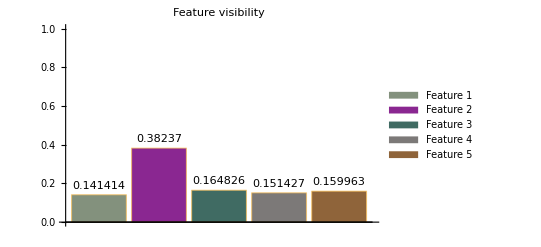

{0.0778709,0.159409,0.0774234,0.0956878,0.0895883}

-Graphics-

{0.205919,0.297472,0.157804,0.174241,0.164563}

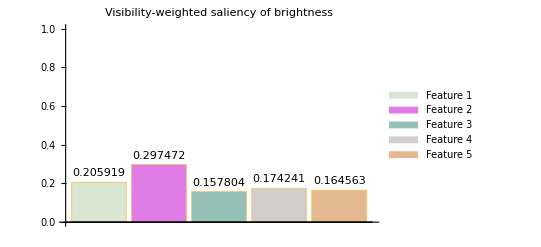

{0.0566026,0.689225,0.0858356,0.00639389,0.161943}

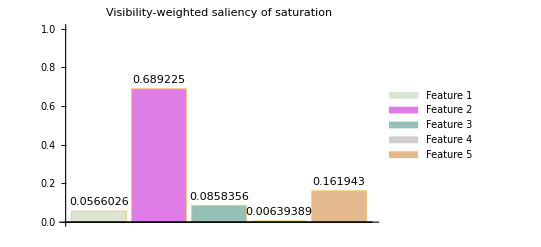

{0.131261,0.493349,0.12182,0.0903175,0.163253}

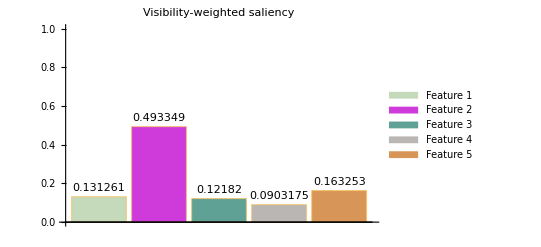

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of RegularExpression[https?://.*].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[Import::nffil :  File not found during Import.]

AssociateTo::invak: The argument scoremap is not a valid Association.

```mathematica
facename=Last@face;
vis=renderslices[facename];
visibility=ParallelTable[ImageMeasurements[ImageMultiply[vis,features[[i]]],"TotalIntensity"]/ImageMeasurements[vis,"TotalIntensity"],{i,Length[features]}]
chart1=BarChart[visibility,PlotLabel->"Feature visibility",ChartLegends->legends,ChartStyle->(chartcolors//Darker),ChartLabels->Placed[ToString/@visibility,Above],PlotRange->{Automatic,{0,1}}]
dog=g1;
saliency=ParallelTable[ImageMeasurements[ImageMultiply[dog,features[[i]]],"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"],{i,Length[features]}]
chart0=BarChart[saliency,PlotLabel->"Feature saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@saliency,Above],PlotRange->{Automatic,{0,1}}]
viss=ImageMultiply[dog,vis];
vs=ParallelTable[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}]
chart2=BarChart[vs,PlotLabel->"Visibility-weighted saliency of brightness",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs,Above],PlotRange->{Automatic,{0,1}}]
viss2=ImageMultiply[g2,vis];
vs2=ParallelTable[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}]
chart2b=BarChart[vs2,PlotLabel->"Visibility-weighted saliency of saturation",ChartLegends->legends,ChartStyle->(chartcolors//Lighter),ChartLabels->Placed[ToString/@vs2,Above],PlotRange->{Automatic,{0,1}}]
mean=Mean[{vs,vs2}]
weighted=BarChart[mean,PlotLabel->"Visibility-weighted saliency",ChartLegends->legends,ChartStyle->chartcolors,ChartLabels->Placed[ToString/@mean,Above],PlotRange->{Automatic,{0,1}}]
charts={chart0,chart1,chart2,chart2b,weighted};
scores={saliency,visibility,vs,vs2,mean};
imagefilenames2=StringReplace[#,"."->"_"<>facename<>"."]&/@imagefilenames;
txtfilenames2=StringReplace[#,"."->"_"<>facename<>"."]&/@txtfilenames;
Table[Export[imagefilenames2[[i]],charts[[i]]],{i,Length[charts]}];
(*Table[Export[txtfilenames2[[i]],scores[[i]]],{i,Length[scores]}];*)
scoremap=If[FileExistsQ[resultxml],Association@Import[resultxml],<||>];
AssociateTo[scoremap,(dataname<>"_"<>facename)->scores];
Export[resultxml,Normal[scoremap]];
w=ImageAdd[viss,viss2]//ImageAdjust;
results=ImageMultiply[w,#]&/@features;
MapIndexed[Export[StringReplace[featurefilename,"."->ToString[First[#2]]<>"_"<>facename<>"."],#]&,results];
```

```mathematica
(*ParallelTable[ImageApply[#*#2*#3&,{dog,features[[i]],vis}],{i,Length[features]}]*)
```

```mathematica
Norm[List@@#]&/@ColorConvert[chartcolors,"LCH"]
```

{0.936125,1.3669,0.831608,0.757736,0.847053}

```mathematica
Norm[List@@#]&/@ColorConvert[chartcolors,"LAB"]
```

{0.861945,1.02841,0.661323,0.7436,0.827855}